## Инициализация

```mathematica
λ=820 10^-9;
k=(2 π)/λ;
Ml[l_]:=({{1, l}, {0, 1}}); (*Возвращает матрицу для распространения пучка на l м*)
Mf[f_]:=({{1, 0}, {-1/f, 1}});(*Матрица для прохождения пучка через линзу с f=f м*)
ReverseM[M_]:=({{-M[[2,2]], M[[1,2]]}, {M[[2,1]], -M[[1,1]]}}); (*Матрица обратного преобразования*)
ApplyM[q_,M_]:=(M[[1,1]] q +M[[1,2]])/(M[[2,1]] q+M[[2,2]]); (*Применить преобразование M к q*)
W[Q_]:=N[(Im[1/Q] k)^-0.5];(*Полуширина пучка*)
A[Q_]:=N[√((-Im[Q])/k)];(*Полуширина перетяжки пучка*)
(*Reminder: матрицы перемножаются в обратном порядке! Оператор перемножения матриц в математике - точка!*)
```

## Вычисление необходимого на входе в резонатор пучка

```mathematica
(*В первой версии удвоителя длина волны была 1120нм, и длина кристала l0, полуширина перетяжки w0=17*10^-6. Величина lλ/w0^2 должна остаться константой=> w∝√(l/l0*λ/λ0)*)
(*Считаем пучок на выходе из резонатора*)
Subscript[q, 0]=-I k (17 10^-6 *√(1/1.5*λ/(1120 10^-9)))^2;
(*поворачиваем ось z в конце q=dZ - ib)=> надо взять сопряжение и минус*)
Subscript[Q, RX]=N[-ApplyM[Subscript[q, 0],Ml[156 10^-3].Mf[(40 10^-3)/2 Cos[8/180 π]^-1].Ml[23 10^-3]]*]
Subscript[Q, RY]=N[-ApplyM[Subscript[q, 0],Ml[156 10^-3].Mf[(40 10^-3)/2 Cos[8/180 π]].Ml[23 10^-3]]*]
(*Значит, пучок должен быть чуть сходящимся, и перетяжка на 3-5 см уходит внутрь резонатора*)
(*Размер пучка в перетяжке:*)
"Перетяжка пучка, входящего в резонатор, ось x"
W[Subscript[Q, RX]]
"Перетяжка пучка, входящего в резонатор, ось y"
W[Subscript[Q, RY]]
```

-0.00913284-0.0488373 ⅈ

-0.0260216-0.0372754 ⅈ

Перетяжка пучка, входящего в резонатор, ось x

0.0000812189

Перетяжка пучка, входящего в резонатор, ось y

0.0000850613

```mathematica
A[Subscript[Q, RX]]
```

0.0000798349

## Вычисление параметров пучка лазера

```mathematica
(*Вычисление параметров Subscript[Q, LX], Subscript[Q, LY] лазера. z1 и z2 - расстояния от лазера до двух точек измерения. dij - ПОЛУширина(то есть то что в формуле фита b*Exp[-(t-c)^2/d^2]) пучка в точке i по оси j. Все величины в метрах*)
z1=0.09;
z2=0.24;
d1x=93.46314099675452 10^-5;
d1y=85.5121255812608 10^-5;
d2x=210.25427477401226 10^-5;
d2y=187.54700595289762 10^-5;
LasQxSol=Solve[{W[ApplyM[Qx,Ml[z1]]]==d1x,W[ApplyM[Qx,Ml[z2]]]==d2x},Qx];
LasQySol=Solve[{W[ApplyM[Qy,Ml[z1]]]==d1y,W[ApplyM[Qy,Ml[z2]]]==d2y},Qy];
Subscript[Q, LX]=Qx/.LasQxSol
Subscript[Q, LY]=Qy/.LasQySol
(*Subscript[Q, LF] - то, что реально будет согласовываться с резонатором. Можно выбрать Subscript[Q, LX] или Subscript[Q, LY], если пучок уже исправлен на астигматизм, можно какие-то средние величины*)
Subscript[Q, LF]=Last[Subscript[Q, LX]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.136159-0.000318336 ⅈ,0.0300109-0.00215246 ⅈ}

{-0.136974-0.000393837 ⅈ,0.0356641-0.00281981 ⅈ}

0.0300109-0.00215246 ⅈ

## Подбор линз

```mathematica
a=.
b=.
c=.
(*Для начала пробуем двухлинзовую схему.*)
PL={40,50,60,75,100,125,150,175,200,250,300,400,500,750,1000};
NL={-50,-100};
PL=Function[x,N[x/1000]]/@PL;
NL=Function[x,N[x/1000]]/@NL;
AL=Join[PL,NL];
(*Вычисление всех возможных комбинаций линз*)
(*В качестве фиксированного параметра берется c - расстояние между лазером и резонатором. Полученные комбинации сразу проверяются на то, чтобы расстояние между линзами было больше 2см, а расстояние между последней линзой и резонатором - больше 20см, чтобы было куда засунуть юстировочные зеркала*)
LenseRules={c->0.5};
Print["f1\tf2"];
Do[
Do[
Coup2Sol=Solve[ {(ApplyM[Subscript[Q, LF],Ml[c-b].Mf[Subscript[f, 2]].Ml[b-a].Mf[Subscript[f, 1]].Ml[a]] ==Subscript[Q, RX]),Im[b]==0,Im[a]==0,Re[a]>0.05,Re[b-a]>0.02,Re[c-b]>0.2}/.LenseRules,{a,b}];
If[Length[Coup2Sol]>0,Print[Subscript[f, 1],"\t",Subscript[f, 2],"\t"];Do[Print[i,"\t"],{i,Coup2Sol}]]
,{Subscript[f, 2],AL}],
{Subscript[f, 1],AL}]
```

f1	f2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.04	0.04

{a→0.0709722,b→0.182603}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.04	0.05

{a→0.0559333,b→0.189664}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

0.05	0.04

{a→0.0865137,b→0.220245}

0.05	0.05

{a→0.0690521,b→0.230361}

0.05	0.06

{a→0.0552537,b→0.25318}

0.05	-0.05

{a→0.108061,b→0.142347}

0.06	0.04

{a→0.0981631,b→0.258113}

0.06	0.05

{a→0.0777641,b→0.275691}

0.06	-0.05

{a→0.12624,b→0.180112}

0.06	-0.1

{a→0.0905412,b→0.130601}

0.075	0.75

{a→0.0538256,b→0.189591}

0.075	1.

{a→0.0558538,b→0.210878}

0.075	-0.05

{a→0.148131,b→0.23519}

0.075	-0.1

{a→0.110603,b→0.195058}

0.1	0.25

{a→0.0549825,b→0.0853331}

## Тест полученных результатов

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.0709722,b→0.182603}}

Distance between last lense and resonator

0.317397

Distance between lenses

0.111631

Beam Waist

79.8349

Distance between first lense and waist

0.0662041

Distance between second lense and waist

0.32653

Plot::plln: Limiting value 0.1  + Re[c] in {x, 0, Re[c + 0.1]} is not a machine-sized real number.

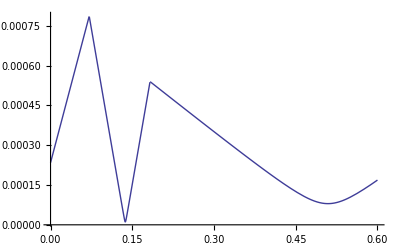

```mathematica
(*Потестим полученные величины. Подставляешь выбранные фокусные расстояния и можешь варьировать Subscript[Q, F] - пучок на входе в резонатор. Двигать и изменять размер перетяжки.
Он выводит получающиеся при этом положения линз, график ширины пучка, а также инфу, полезную для юстировки - расстояние между линзами, расстояние до перетяжки после каждой линзы(т.е. когда юстируешь - ставишь линзы по одной и следишь, чтобы перетяжка оказалась от линзы именно на этом расстоянии. Иногда там просто все довольно чувствительно и это довольно удобный критерий)*)
x=.
TestSolRules={First[LenseRules],Subscript[f, 1]->0.04,Subscript[f, 2]->0.04,Subscript[Q, F]->Subscript[Q, RX]};
sol1=Solve[ {(ApplyM[Subscript[Q, LF],Ml[c-b].Mf[Subscript[f, 2]].Ml[b-a].Mf[Subscript[f, 1]].Ml[a]] ==Subscript[Q, F]),Im[b]==0,Im[a]==0,Re[a]>0.05,Re[b-a]>0.02,Re[c-b]>0.2}/.TestSolRules,{a,b}]
"Distance between last lense and resonator"
N[c-b]/.Join[TestSolRules,Last[sol1]]
"Distance between lenses"
N[b-a]/.Join[TestSolRules,Last[sol1]]
"Beam Waist"
A[Subscript[Q, F]]*10^6/.TestSolRules
"Distance between first lense and waist"
N[-Re[ApplyM[Subscript[Q, LF],Mf[Subscript[f, 1]].Ml[a]]]/.Join[TestSolRules,First[sol1]]]
"Distance between second lense and waist"
N[-Re[ApplyM[Subscript[Q, LF],Mf[Subscript[f, 2]].Ml[b-a].Mf[Subscript[f, 1]].Ml[a]]]/.Join[TestSolRules,First[sol1]]]
(Plot[
Piecewise[{
{W[ApplyM[Subscript[Q, LF],Ml[x]]],x<a},
{W[ApplyM[Subscript[Q, LF],Ml[Re[x-a]].Mf[Subscript[f, 1]].Ml[a]]],a<=x<Re[b]},
{W[ApplyM[Subscript[Q, LF],Ml[Re[x-b]].Mf[Subscript[f, 2]].Ml[Re[b-a]].Mf[Subscript[f, 1]].Ml[a]]],Re[b]<=x<Re[c+0.1]}
}],{x,0,Re[c+0.1]},PlotRange->Full])/.Join[TestSolRules,sol1[[1]]]
```

{a→0.0612,f_1→0.04,b→0.1777,f_2→0.04,c→0.5}

-0.00162519-0.0700691 ⅈ

Plot::plln: Limiting value 0.1  + Re[c] in {x, 0, Re[c + 0.1]} is not a machine-sized real number.

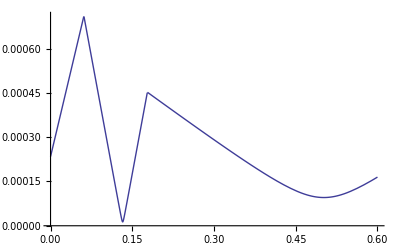

-0.000291907+0.0104206 ⅈ

Перетяжка итогового пучка

0.+0.0000368777 ⅈ

Ширина пучка в центре кристалла

2.25899×10^-21-0.0000368921 ⅈ

```mathematica
(*И тут уже совсем безбашенные тесты. Просто смотрим что получится на кристале при установке линз произвольным образом*)
CrazyRules={a->0.0612,Subscript[f, 1]->0.04,b->0.1777,Subscript[f, 2]->0.04,c->0.5}
(*Вот это будет на входе в резонатор*)
Subscript[Q, CR]=ApplyM[Subscript[Q, LF],Ml[c-b].Mf[Subscript[f, 2]].Ml[b-a].Mf[Subscript[f, 1]].Ml[a]]/.CrazyRules
(Plot[
Piecewise[{
{W[ApplyM[Subscript[Q, LF],Ml[x]]],x<a},
{W[ApplyM[Subscript[Q, LF],Ml[Re[x-a]].Mf[Subscript[f, 1]].Ml[a]]],a<=x<Re[b]},
{W[ApplyM[Subscript[Q, LF],Ml[Re[x-b]].Mf[Subscript[f, 2]].Ml[Re[b-a]].Mf[Subscript[f, 1]].Ml[a]]],Re[b]<=x<Re[c+0.1]}
}],{x,0,Re[c+0.1]},PlotRange->Full])/.Join[CrazyRules]
Subscript[Q, CRC]=ApplyM[Subscript[Q, CR],Ml[23 10^-3]Mf[(40 10^-3)/2 Cos[8/180 π]^-1].Ml[156 10^-3]]
"Перетяжка итогового пучка"
A[Subscript[Q, CRC]]
"Ширина пучка в центре кристалла"
W[Subscript[Q, CRC]]
```